```mathematica
countryWideConfirmed=Import["~/projects/VirusStuff/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv","CSV"];
```

```mathematica
countryWideConfirmedExChina = DeleteCases[countryWideConfirmed,{_,"China",__}];
countryWideConfirmedExChina=Drop[countryWideConfirmedExChina,1,{1,4}];
```

```mathematica
globalConfirmedExChina = Transpose[{Total[countryWideConfirmedExChina,{1}]}];
data=MapThread[Prepend,{globalConfirmedExChina,Table[a,{a,0,Length[globalConfirmedExChina]-1,1}]}]
```

{{0,7},{1,11},{2,21},{3,28},{4,43},{5,50},{6,69},{7,79},{8,93},{9,125},{10,147},{11,157},{12,165},{13,185},{14,195},{15,207},{16,281},{17,306},{18,321},{19,408},{20,416},{21,462},{22,473},{23,527},{24,617},{25,711},{26,824},{27,925},{28,1020},{29,1120},{30,1269},{31,1571},{32,1936},{33,2320},{34,2652},{35,3222},{36,4146},{37,5184},{38,6655},{39,8437},{40,10170},{41,12579},{42,14734},{43,17345},{44,21104},{45,25061},{46,28982},{47,32711},{48,37715},{49,44954},{50,47421},{51,64264},{52,75127},{53,86451},{54,100540},{55,116092},{56,133807},{57,161550},{58,190914},{59,223214},{60,255654},{61,297049}}

20.2232 ⅇ^(0.157482 t)

(2.7911×10^6)/(1+100.086 ⅇ^(7.64867-0.166063 t))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c[t]→(1. ⅇ^(0.179211 t) k)/(1. ⅇ^(0.179211 t)-0.142857 (7.-1. k)^1.)}}

FittedModel[(1.17882×10^6 ⅇ^(«20» t))/(168401.+1. ⅇ^(«20» t))]

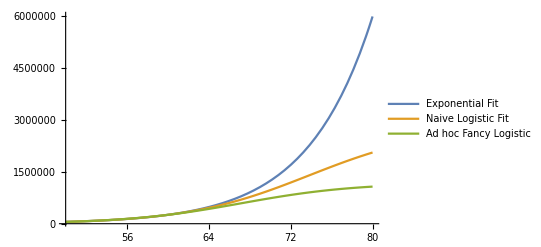

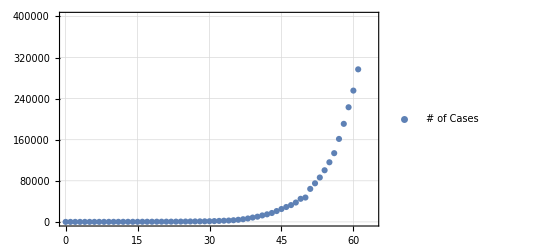

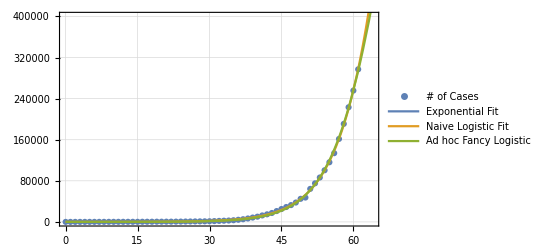

```mathematica
fit=NonlinearModelFit[data,a Exp[-b t],{a,b,c},t];
fit2=NonlinearModelFit[data,c/(1+a*Exp[-b t+d]),{a,b,c,d},t];
Normal[fit]
Normal[fit2]
sol=DSolve[{c'[t]==1/5.58*c[t]*(1-(c[t]/k)),c[data[[1,1]]]==data[[1,2]]},c[t],t]
fit3=NonlinearModelFit[data,c[t]/.sol,k,t]
Plot[{Normal[fit],Normal[fit2],Normal[fit3]},{t,50,80},PlotRange->All,PlotLegends->{"Exponential Fit","Naive Logistic Fit","Ad hoc Fancy Logistic"}]
scatterPlot=ListPlot[data,PlotRange->{{0,64},{0,400000}},Frame->True,GridLines->Automatic,PlotLegends->{"# of Cases"}]
fitPlots=Plot[{Normal[fit],Normal[fit2],Normal[fit3]},{t,0,1000},PlotRange->All,PlotLegends->{"Exponential Fit","Naive Logistic Fit","Ad hoc Fancy Logistic"}];
Show[scatterPlot,fitPlots]
```